## 3.029 Spring 2022 Assignment 01 Due February 17th at 1pm

## Computational Classical Mechanics

## General Instructions Reminder

Notebooks should be submitted to canvas

You can choose to submit either a Wolfram Notebook (.nb), or  a Jupyter Notebook (.ipynb)

Please name your notebook using the following notation:
3029__Assignment-01__LASTNAME_FIRSTNAME.nb

Before submitting your notebook:

Make sure all your code runs from a fresh kennel 
Wolfram Notebook: Evaluation → Quit Kernel, Evaluation → Evaluate Notebook
Jupyter Notebook: Kernel → Restart & Run All

Delete all your output
Wolfram Notebook: Cell → Delete All Output
Jupyter Notebook: Cell → All Output → Clear

Tips to maximize your score:

Comment your code well using text cells/Markdown (not in-line comments)

Don’t include extraneous code and narrative that does not contribute to the answer

But feel free to keep a ‘scratch’ notebook as you develop your solutions

Make your graphics aesthetically pleasing and easy to read

Notably: label your axes and use legible font sizes

## Double Pendulum & Chaotic Systems (25 points)

In mathematics, chaotic systems are those which show a sensitive dependence on initial conditions,

or in the words of Edward Lorenz
“Chaos: when the present determines the future, but the approximate present does not approximately determine the future

The double pendulum is one of the simplest dynamical systems with chaotic solutions

Recall we investigated the dynamics of the double pendulum in lecture 02 using Hamiltonian mechanics

To obtain animations such as the one below

### Small-angle approximation (10 points)

Solve the double pendulum for small initial displacements (e.g. θ_1=θ_2=π/36)

Animate your solution in time, like we did in class - with one additional panel plotting θ_1(t) vs θ_2(t) as the system evolves

Hint: Look at ParametricPlot

Do the same for successively larger and larger initial displacements

Comment on your visualization and results

### Sensitivity to initial conditions (15 points)

Solve two different sets of double pendulum with the following initial displacements (or another equally close set)

Simulation 01: θ_1=π/2,θ_2=-π/2

Simulation 02: θ_1=π/2,θ_2=-π/2+10^-6

Animate both sets of pendula in time (using different colors to differentiate them)

Comment on how sensitive your simulations are to the perturbation we made in initial conditions

Find an appropriate metric to quantify how “different” the two solutions are and plot this over time

Hint: Think about Log-Log, Log-Linear, Linear-Log plots to show the difference clearly

## Normal Modes (75 points)

We’ll investigate the normal modes of coupled oscillators confined on a ring

We will use the angles θ_i as our generalized coordinates

And consider evenly-spaced oscillators as our equilibrium conditions

E.g. for 5 oscillators we would have something like

```mathematica
equilibriumPositionsFive=Most[Range[0,2π,2π/5]]
```

{0,(2 π)/5,(4 π)/5,(6 π)/5,(8 π)/5}

Here’s a simple utility function to draw these

```mathematica
coupledOscillators[positions_,{r_,δr_}]:=Graphics[{
Red,Circle[{0,0},r],Black,
Disk[r{Cos[#],Sin[#]},2δr]&/@positions},
PlotRange->(r+2δr){{-1,1},{-1,1}},ImageSize->150
]
```

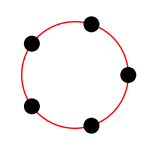

```mathematica
coupledOscillators[equilibriumPositionsFive,{1,0.075}]
```

In what follows, start with  (it’ll be easier to work out the math, and it generalizes easily to larger N)

### Lagrangian & Hamiltonian (10 points)

Write down the system Lagrangian (in terms of θ_i and (θ̇)_i)

Write down the system Hamiltonian (in terms of θ_i and (θ̇)_i)

Express the canonical momenta p_i in terms of θ_i and (θ̇)_i

Use these substitutions to write down the canonical Hamiltonian (in terms of θ_i and p_i)

Comment on your result - was there an easier way to get these?

### Equations of Motion (10 points)

Write down Hamilton’s equations of motion

Hint: That’s 2 equations for each oscillator

Combine Hamilton’s equations to derive the equations of motion

### Educated Guess (15 points)

Make an educated guess (ansatz) as to kind of solutions we expect to get

Hint: We’ve seen masses on springs evolve periodically in time

Substitute your guess into the equations of motion above to obtain  equations of motion

You should have   equations of motion, each depending on a subset of your  variables

Express this as matrix of equations, such that when dotted with your variables it recovers your  equations

E.g. if your equations were (this is for demonstration only)

```mathematica
dummyEquations={
θ1+2θ2==0,
2θ1+3θ2==0
};
```

Then you can obtain your matrix using

```mathematica
variables={θ1,θ2};
MatrixForm[matrix=Normal[Last[CoefficientArrays[dummyEquations,variables]]]]
matrix.variables
```

(1 | 2
2 | 3)

{θ1+2 θ2,2 θ1+3 θ2}

### Eigenvalue Problem (25 points)

Inspecting your matrix you should see that it has the form of an eigenvalue problem

I.e. it looks like

where  is your matrix,  is the identity,  are your variables, and   is the eigenvalue

One way to solve this would be to set the determinant of the matrix you computed above to zero

A different way, would be to define a new matrix by adding  and using Eigensystem

Hint:  will be the common element along your matrix’s diagonal

Once you have this matrix, evaluate it numerically (e.g. pick the spring constant  and set all masses to 1)
and then pass it in the utility function below

```mathematica
orthogonalEigenSystem[numericalMatrix_?(MatrixQ[#,NumericQ]&)]:=Block[{evals,evecs},
{evals,evecs}=Eigensystem[numericalMatrix];
{evals, Flatten[Orthogonalize/@FindClusters[evals->evecs],1]}]
```

The function will return a list of two elements:
the first will be a list of the  eigenvalues
the second will be a matrix where the i^th row is the i^th eigenvector

Note: this is to ensure your eigenvectors are orthogonal - If you find yourself stuck at this point, please ask!

Comment on your eigenvalues!

### Visualization (15 points)

Substitute your solutions back into your the educated guess and animate your result as a function of time!

Here are a number of hints:

You should find that for one of the eigenvalue solutions, your ansatz is non-unique. 
Don’t worry, this is correct - and thinking about what that eigenvalue means physically will help you find a workaround

Your solutions should be complex in character - which part should you use? Real or Imaginary? (Pick the one which agrees with your initial conditions for t=0)

Please ask if you get stuck!